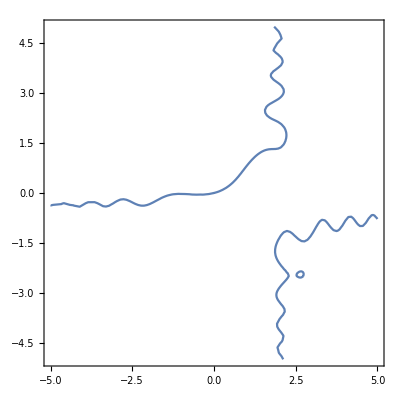

```mathematica
ContourPlot[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{x,-5,5},{y,-5,5}]
```

```mathematica
D[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{y,2},NonConstants->{x}]
```

-4 y^2 Cos[y^2]+4 D[x,y,NonConstants→{x}]+2 Cos[x^2] D[x,y,NonConstants→{x}]^2+D[x,{y,2},NonConstants→{x}]+2 y D[x,{y,2},NonConstants→{x}]+2 x Cos[x^2] D[x,{y,2},NonConstants→{x}]-4 x^2 D[x,y,NonConstants→{x}]^2 Sin[x^2]-2 Sin[y^2]==0

```mathematica
f[c_]=D[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{y,c},NonConstants->{x}]
```

D[x-4 y+2 x y+Cos[y^2]+Sin[x^2]==1,{y,c},NonConstants→{x}]

```mathematica
D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2},x[y]]
```

-12 Sin[x[y]^2] x[y] x'[y]^2-8 Cos[x[y]^2] x[y]^3 x'[y]^2+2 Cos[x[y]^2] x''[y]-4 Sin[x[y]^2] x[y]^2 x''[y]==0

```mathematica
Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2}],x''[y]]/.{y->0, x[y]-> 0, x'[y]->4}
```

{{x''[0]→-48}}

```mathematica
Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2}],x''[y]]
```

{{x''[y]→(2 (2 y^2 Cos[y^2]+Sin[y^2]-2 x'[y]-Cos[x[y]^2] x'[y]^2+2 Sin[x[y]^2] x[y]^2 x'[y]^2))/(1+2 y+2 Cos[x[y]^2] x[y])}}

```mathematica
f[c_]=Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,c}],D[x[y],{y,c}]]
```

Solve::naqs: ∂_{y,c} (-4 y+Cos[y^2]+Sin[x[y]^2]+x[y]+2 y x[y]==1) is not a quantified system of equations and inequalities.

Solve[∂_{y,c} (-4 y+Cos[y^2]+Sin[x[y]^2]+x[y]+2 y x[y]==1),x^(c)[y]]

```mathematica
f[2]
```

{{x''[y]→(2 (2 y^2 Cos[y^2]+Sin[y^2]-2 x'[y]-Cos[x[y]^2] x'[y]^2+2 Sin[x[y]^2] x[y]^2 x'[y]^2))/(1+2 y+2 Cos[x[y]^2] x[y])}}

```mathematica
f[1]/.{y->0, x[y]-> 0}
```

{{x'[0]→4}}

```mathematica
f[2]/.{y->0, x[y]-> 0,D[x[y],{y,1}]->Values[(f[1]/.{y->0, x[y]-> 0})]}
```

{{x''[0]→{{-48}}}}

```mathematica
f[3]/.{y->0, x[y]-> 0,D[x[y],{y,1}]->Values[(f[1]/.{y->0, x[y]-> 0})],D[x[y],{y,2}]->Values[f[2]/.{y->0, x[y]-> 0,D[x[y],{y,1}]->Values[(f[1]/.{y->0, x[y]-> 0})]}]}
```

{{x^(3)[0]→{{{{1440}}}}}}